Power::infy: 無限式1/0.が見付かりました．

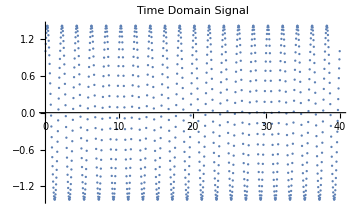
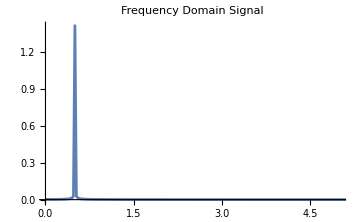
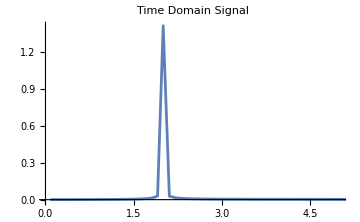

```mathematica
(*check*)
ClearAll["Global`*"];
ClearAll["Global`*"];
T=2.;
n=1000;
span=20*T;
data=Table[{t,Sin[t*2 π/T]+Cos[t*2 π/T]},{t,Subdivide[0,span,n-1]}];
(*Calculate the FFT magnitude without any additional normalization*)
fft=2*Abs@Fourier[data[[;;-1,2]],FourierParameters->{-1, 1}];

(*Calculate the frequency bins*)
Fs=n/span;
freq=Table[i*Fs/n,{i,0,n/2-1}]; (*Positive frequencies*)

{ListPlot[data,ImageSize->Medium,PlotLabel->"Time Domain Signal"],
ListPlot[Transpose[{freq,fft[[;;n/2]]}],Joined->True,PlotRange->{{0,5},All},ImageSize->Medium,PlotLabel->"Frequency Domain Signal"],
ListPlot[Transpose[{1/freq,fft[[;;n/2]]}],Joined->True,PlotRange->{{0,5},All},ImageSize->Medium,PlotLabel->"Time Domain Signal"]}
```

```mathematica
ClearAll["Global`*"];
storage="/Volumes/home/BEM/202309/";
```

```mathematica
case="moon_pool_large_a0d8_";
name="large"
data[name][5.0]=Import[storage<>case<>"T5d0_h80/result.json"];
data[name][5.5]=Import[storage<>case<>"T5d5_h80/result.json"];
data[name][6.0]=Import[storage<>case<>"T6d0_h80/result.json"];
data[name][6.5]=Import[storage<>case<>"T6d5_h80/result.json"];
data[name][7.0]=Import[storage<>case<>"T7d0_h80/result.json"];
data[name][7.5]=Import[storage<>case<>"T7d5_h80/result.json"];
data[name][8.0]=Import[storage<>case<>"T8d0_h80/result.json"];
data[name][8.5]=Import[storage<>case<>"T8d5_h80/result.json"];
data[name][9.0]=Import[storage<>case<>"T9d0_h80/result.json"];
data[name][9.5]=Import[storage<>case<>"T9d5_h80/result.json"];
data[name][10.0]=Import[storage<>case<>"T10d0_h80/result.json"];


case="moon_pool_no_a0d8_";
name="no"
data[name][5.0]=Import[storage<>case<>"T5d0_h80/result.json"];
data[name][5.5]=Import[storage<>case<>"T5d5_h80/result.json"];
data[name][6.0]=Import[storage<>case<>"T6d0_h80/result.json"];
data[name][6.5]=Import[storage<>case<>"T6d5_h80/result.json"];
data[name][7.0]=Import[storage<>case<>"T7d0_h80/result.json"];
data[name][7.5]=Import[storage<>case<>"T7d5_h80/result.json"];
data[name][8.0]=Import[storage<>case<>"T8d0_h80/result.json"];
data[name][8.5]=Import[storage<>case<>"T8d5_h80/result.json"];
data[name][9.0]=Import[storage<>case<>"T9d0_h80/result.json"];
data[name][9.5]=Import[storage<>case<>"T9d5_h80/result.json"];
data[name][10.0]=Import[storage<>case<>"T10d0_h80/result.json"];

(*Recreate*)
dt=0.01;
min=0;
max=100;

Do[
Print["make data of ",name," T=",T];
DATA=data[name][T];
Time[name][T]=Table[t,{t,min,max,dt}];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,("floatingbody_pitch"/.DATA)}]];
Pitch[name][T]=Table[tmp[t],{t,min,max,dt}];
];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,(("floatingbody_COM"/.DATA)ᵀ[[3]]-75)}]];
Heave[name][T]=Table[tmp[t],{t,min,max,dt}];
];
Module[{tmp},
tmp=Interpolation[Transpose[{"time"/.DATA,(("floatingbody_COM"/.DATA)ᵀ[[1]]-200)}]];
Surge[name][T]=Table[tmp[t],{t,min,max,dt}];
]
,{name,{"no","large"}},{T,5.0,10.0,.5}]

dataLen[T_]:=Length[Table[t,{t,min,max,dt}]];

fftPitch[name_][T_]:=With[{n=Length[Time[name][T]]},Return[2*Abs@Fourier[Pitch[name][T][[;;-1]],FourierParameters->{-1, 1}]];];
fftHeave[name_][T_]:=With[{n=Length[Time[name][T]]},Return[2*Abs@Fourier[Heave[name][T][[;;-1]],FourierParameters->{-1, 1}]];];
fftSurge[name_][T_]:=With[{n=Length[Time[name][T]]},Return[2*Abs@Fourier[Surge[name][T][[;;-1]],FourierParameters->{-1, 1}]];];

getPeriod[name_][T_]:=1/Table[i/(max-min),{i,Length[fftPitch[name][T]]}];
getTime[name_][T_]:=Module[{},Return[(Time[name][T])];];
(*ListPlot[Table[Transpose[{Table[i/(max-min),{i,Length[fftPitch[T]]}],fftPitch[T]}][[;;20]],{T,5.5,10.,0.5}],PlotRange->All,Joined->True]*)
```

large

no

make data of no T=5.

InterpolatingFunction::dmval: 入力値{0.}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{0.01}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{0.02}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

make data of no T=5.5

make data of no T=6.

make data of no T=6.5

make data of no T=7.

make data of no T=7.5

make data of no T=8.

make data of no T=8.5

make data of no T=9.

make data of no T=9.5

make data of no T=10.

make data of large T=5.

make data of large T=5.5

make data of large T=6.

make data of large T=6.5

make data of large T=7.

make data of large T=7.5

make data of large T=8.

make data of large T=8.5

make data of large T=9.

make data of large T=9.5

make data of large T=10.

```mathematica
(*dataLen[T_]:=Length["time"/.data[T]];

Pitch[T_]:=("floatingbody_pitch"/.data[T])[[;;-1]];
Heave[T_]:=("floatingbody_COM"/.data[T])ᵀ[[3]]-75;
Surge[T_]:=(("floatingbody_COM"/.data[T])ᵀ[[1]]-200)[[;;-1]];

fftPitch[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[("floatingbody_pitch"/.data[T])[[;;-1]],FourierParameters->{-1, 1}]];];
fftHeave[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[(("floatingbody_COM"/.data[T])ᵀ[[3]]-75)[[;;-1]],FourierParameters->{-1, 1}]];];
fftSurge[T_]:=With[{n=Length["time"/.data[T]]},Return[2*Abs@Fourier[(("floatingbody_COM"/.data[T])ᵀ[[1]]-200)[[;;-1]],FourierParameters->{-1, 1}]];];
(*getPeriod[data_]:=With[{timelist="time"/.data,n=Length[timelist],dt=0.2},Return@Table[(i/(n*dt))^-1,{i,1,n,1}]];*)
getPeriod[T_]:=Module[{t,n},t="time"/.data[T];n=Length[t];Return@Table[(i/(n*(If[i+1>n,t[[i]]-t[[i-1]],t[[i+1]]-t[[i]]])))^-1,{i,1,n,1}]];
getTime[T_]:=Module[{},Return[("time"/.data[T])];];*)
```

```mathematica
(*Do[data75[[i]][[2]]=data75[[i]][[2]][[;;547]],{i,1,Length[data75]}]*)
```

```mathematica
Column@data[5.0][[;;,1]]
```

Part::partd: 部分指定data[5.]⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Column[data[5.]⟦1;;All,1⟧]

```mathematica
(*Peridos to check*)
Ts={(*5.0,*)5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0,9.5,10.};
```

```mathematica
legend=LineLegend[Table[T,{T,Ts}],LegendLabel->"Incident wave period [s]",LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5,LegendMarkerSize->15,LabelStyle->{15,FontFamily->"Times"}];
commonOptions2D=Sequence[
ImageSize->600,
AspectRatio->1/2,
Joined->True,
Frame->True,
FrameStyle->Directive[{FontSize->20,Black,Thickness[0.002],FontFamily->"Times"}],
PlotStyle->Table[{ColorData[90,"ColorList"][[i]],{Dashed,Normal}[[Mod[i,2]+1]]},{i,1,10}],
AxesStyle->Directive[{FontSize->20,Black,FontFamily->"Times"}],
LabelStyle->Directive[{FontSize->20,Black,FontFamily->"Times"}],
PlotLegends->Placed[legend,Top]
];
commonOptions3D=Sequence[TicksStyle->Black,ImageSize->Medium,AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}]];
```

```mathematica
dir="/Users/tomoaki/Library/CloudStorage/Dropbox/meeting/海洋工学シンポジウム/2023/投稿論文/";
```

## Surge

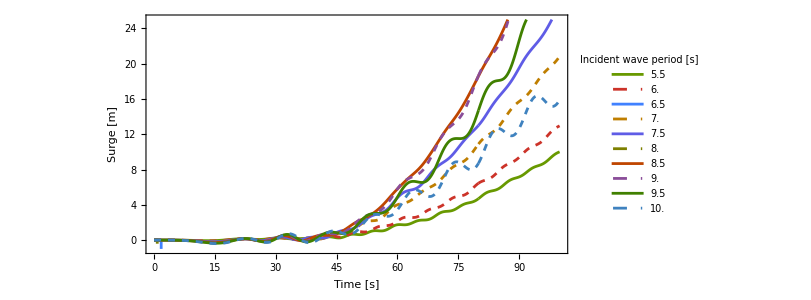
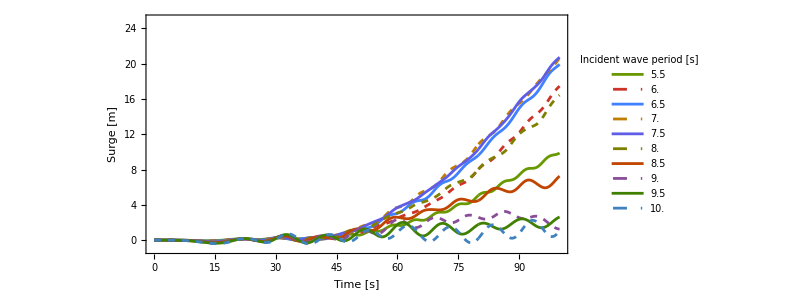

```mathematica
{fig0,fig1}=Table[
ListPlot[Table[Transpose[{getTime[name][T],Surge[name][T]}][[;;Round[dataLen[T]]]],{T,Ts}]
,PlotLegends->Placed[Append[legend,LegendLayout->{"Column",2}],{0.3,0.5}]
,PlotRange->{{0,100},{-1,25}}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
]
,{name,{"no","large"}}
]
(*Export[dir<>"Surge_no.pdf",fig0,"PDF"];
Export[dir<>"Surge_large.pdf",fig1,"PDF"];*)
```

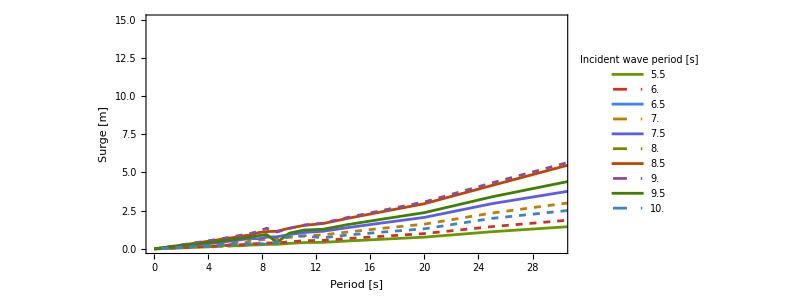
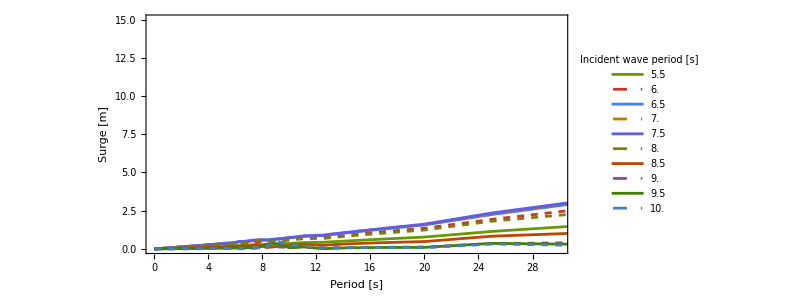

```mathematica
{fig0,fig1}=Table[
ListPlot[Table[Transpose[{getPeriod[name][T],fftSurge[name][T]}][[;;Round[dataLen[T]/2]]],{T,Ts}]
,PlotRange->{{0,30},{0,15}}
,Evaluate@commonOptions2D
,FrameLabel->{"Period [s]","Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
],{name,{"no","large"}}]
(*Export[dir<>"fftSurge_no.pdf",fig0,"PDF"];
Export[dir<>"fftSurge_large.pdf",fig1,"PDF"];*)
```

## Heave

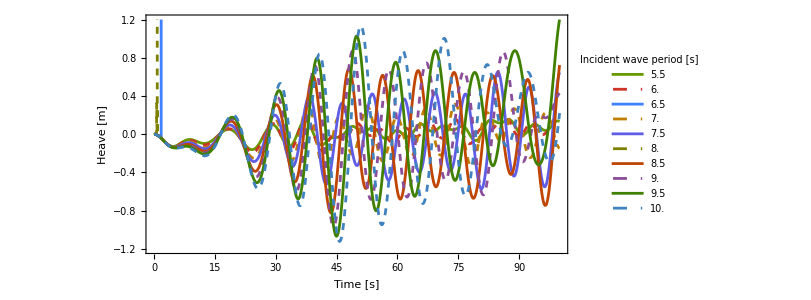
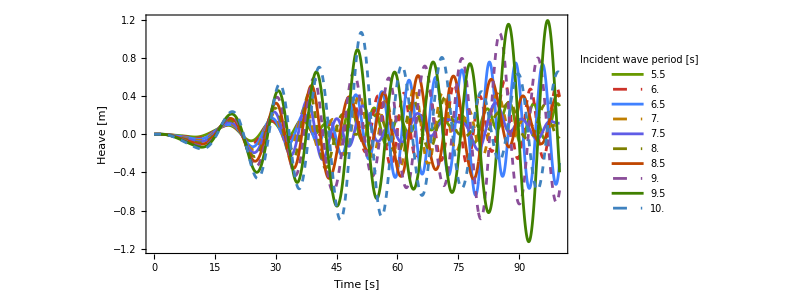

```mathematica
{fig0,fig1}=Table[
ListPlot[Table[Transpose[{getTime[name][T],Heave[name][T]}],{T,Ts}]
,PlotRange->{{0,100},{-1.2,1.2}}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
]
,{name,{"no","large"}}]
(*Export[dir<>"Heave_no.pdf",fig0,"PDF"];
Export[dir<>"Heave_large.pdf",fig1,"PDF"];*)
```

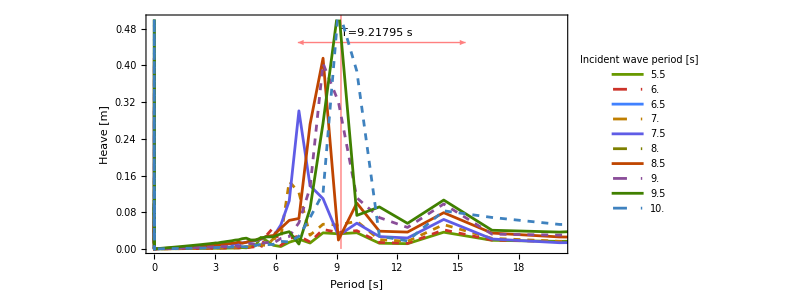
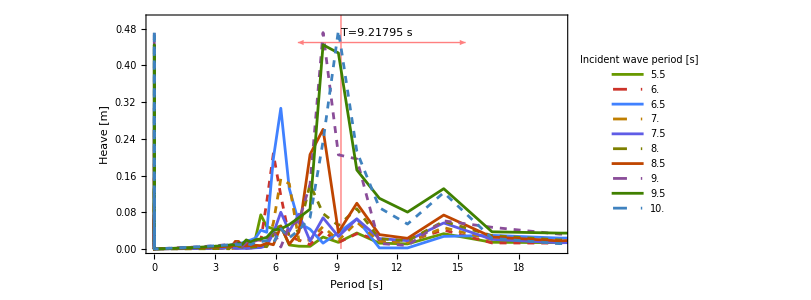

```mathematica
Tpiston=9.21795;
{fig0,fig1}=Table[
ListPlot[Table[Transpose[{getPeriod[name][T],fftHeave[name][T]}],{T,Ts}]
,PlotLegends->Placed[Append[legend,LegendLayout->{"Column",2}],{0.8,0.6}]
,PlotRange->{{0,20},{0,0.5}}
,Evaluate@commonOptions2D
,FrameLabel->{"Period [s]","Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
(*,Prolog->{{LightPink,Rectangle[{0.77*Tpiston,0},{1.67*Tpiston,10}]},{Red,Line[{{Tpiston,0},{Tpiston,10}}]}}*)
 ,Prolog->{{Thick,Pink,Line[{{Tpiston,0},{Tpiston,10}}]},
{Thick,Pink,Arrowheads[{(*{0.02,0},*){0.02,1}}],Arrow[{{Tpiston,0.45},{1/1.3*Tpiston,0.45}}]},
{Thick,Pink,Arrowheads[{(*{0.02,0},*){0.02,1}}],Arrow[{{Tpiston,0.45},{1/0.6*Tpiston,0.45}}]},
(*Rotate[Text["Resonant piston period T="<>ToString[Tpiston]<>" s (Molin, 2001)",{Tpiston,0.3},Center],π/2]*),
Text["T="<>ToString[Tpiston]<>" s",{Tpiston,0.47},Left]}
]
,{name,{"no","large"}}]
(*Export[dir<>"fftHeave_no.pdf",fig0,"PDF"];
Export[dir<>"fftHeave_large.pdf",fig1,"PDF"];*)
```

## Pitch

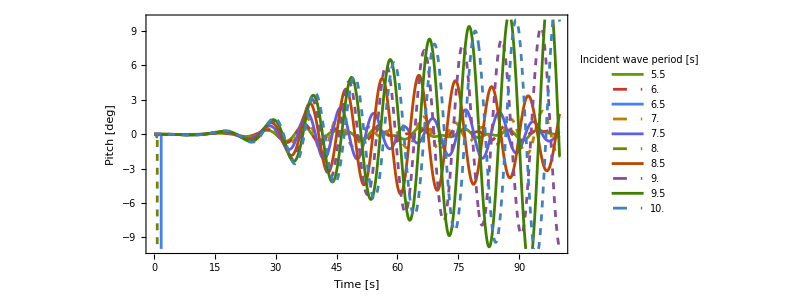
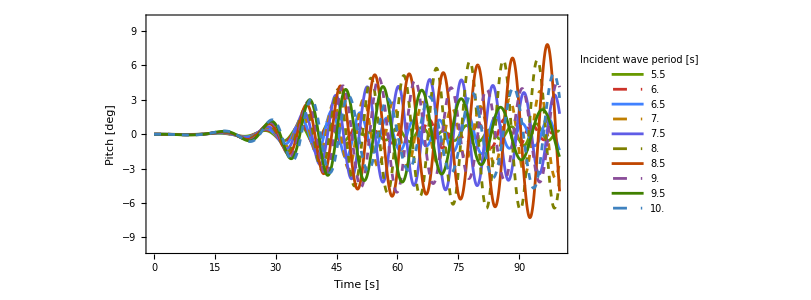

```mathematica
{fig0,fig1}=Table[ListPlot[Table[Transpose[{getTime[name][T],180/Pi*Pitch[name][T]}],{T,Ts}]
,PlotRange->{{0,100},{-10,10}}
,Evaluate@commonOptions2D
,FrameLabel->{"Time [s]","Pitch [deg]"}
],{name,{"no","large"}}]
(*Export[dir<>"Pitch_no.pdf",fig0,"PDF"];
Export[dir<>"Pitch_large.pdf",fig1,"PDF"];*)
```

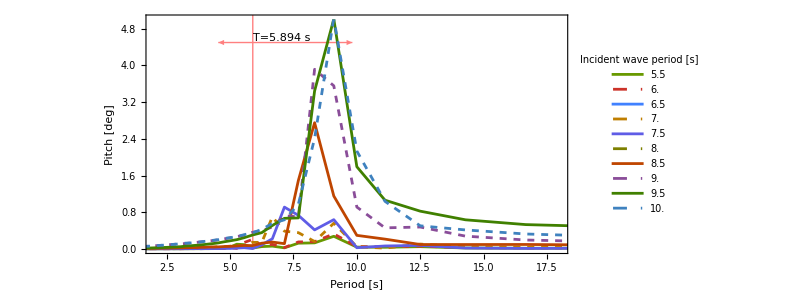
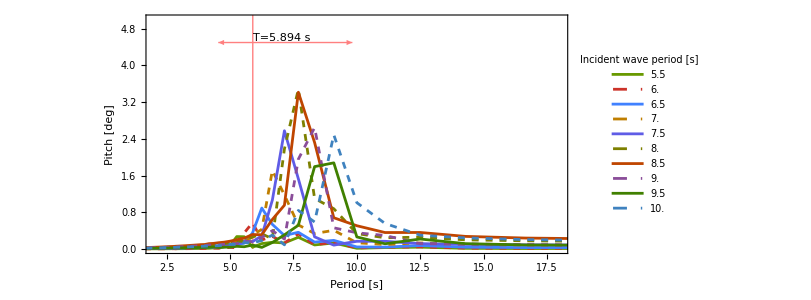

```mathematica
Tl=5.894;
maxPitch=5;
{fig0,fig1}=Table[ListPlot[Table[Transpose[{getPeriod[name][T],180/Pi*fftPitch[name][T]}],{T,Ts}]
,PlotLegends->Placed[legend,{0.72,0.65}]
,PlotRange->{{2,18},{0,maxPitch}}
,Evaluate@commonOptions2D
,FrameLabel->{"Period [s]","Pitch [deg]"}
(*,Prolog->{{LightYellow,Rectangle[{0.77*Tl,0},{1.67*Tl,10}]},{Red,Line[{{Tl,0},{Tl,10}}]}}*)
 ,Prolog->{{Thick,Pink,Line[{{Tl,0},{Tl,10}}]},
{Thick,Pink,Arrowheads[{(*{0.02,0},*){0.02,1}}],Arrow[{{Tl,maxPitch*0.9},{1/1.3*Tl,maxPitch*0.9}}]},
{Thick,Pink,Arrowheads[{(*{0.02,0},*){0.02,1}}],Arrow[{{Tl,maxPitch*0.9},{1/0.6*Tl,maxPitch*0.9}}]},
(*Rotate[Text["Resonant soloshing period T="<>ToString[Tl]<>" s (Molin, 2001)",{Tl,maxPitch*0.5},Center],π/2]*)
Text["T="<>ToString[Tl]<>" s",{Tl,maxPitch*0.92},Left]}
]
,{name,{"no","large"}}]
(*Export[dir<>"fftPitch_no.pdf",fig0,"PDF"];
Export[dir<>"fftPitch_large.pdf",fig1,"PDF"];*)
```